Problem

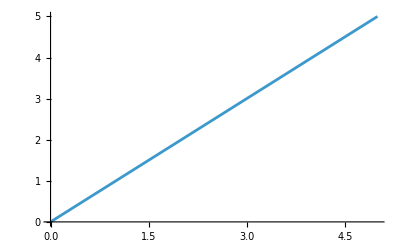

```mathematica
1

Plot [x ,{x,0,5}]
```

```mathematica
2
```

```mathematica
D[f[t],t]
f[t_]:=α*Log[a*t]*Cos[ω*t]*Sin[ω*t]
```

```mathematica
alpha omega Cos[omega t]^2 Log[a t]+(alpha Cos[omega t] Sin[omega t])/t-alpha omega Log[a t] Sin[omega t]^2

D[f[t],{t,2}]
```

alpha omega Cos[omega t]^2 Log[a t]+(alpha Cos[omega t] Sin[omega t])/t-alpha omega Log[a t] Sin[omega t]^2

-alpha omega^2 Cos[omega t] Log[a t] Sin[omega t]-2 alpha omega Sin[omega t] (omega Cos[omega t] Log[a t]+Sin[omega t]/t)+alpha Cos[omega t] ((2 omega Cos[omega t])/t-Sin[omega t]/t^2-omega^2 Log[a t] Sin[omega t])

```mathematica
Clear[f]
3
w[x]=f[x]*g[x]*h[x]
D[w[x],x]
```

3

f[x] g[x] h[x]

g[x] h[x] f'[x]+f[x] h[x] g'[x]+f[x] g[x] h'[x]

```mathematica
4
ell=0.10;
g=9.8;
omega=Sqrt[g/ell];

sol=NDSolve[{phi''[t]==-omega^2 Sin[phi[t]],phi'[0]==0,phi[0]==30 Degree},phi,{t,0,10}]
```

4

{{phi→InterpolatingFunction[…]}}

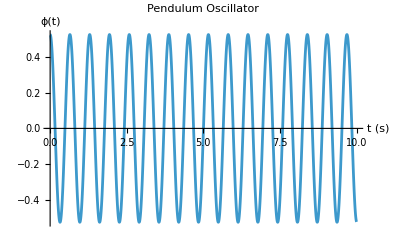

```mathematica
Plot[Evaluate[phi[t]/. sol],{t,0,10},AxesLabel->{"t (s)","ϕ(t)"},PlotLabel->"Pendulum Oscillator"]
```

```mathematica
Graphics3D[{Cylinder[{{0,0,0.25},{0,0,6}},.5],Cylinder[{{0,0,0},{0,0,0.25}},1.5]}]
```

-Graphics3D-